# Heisenberg Animations

## Preamble

This document contains a list of formulas relating to the Heisenberg Group ℍ_1 and a section with computations used for the production of images and animations for the Febraury 22, 2017 Geometry, Topology, and Physics Seminar.

## Formulas

## General Formulas

```mathematica
mag[{x_,y_,t_}]:=√(x^2+y^2+t^2);
```

```mathematica
mag[{x_,y_}]:=√(x^2+y^2);
```

## Basic Formulas for ℍ_1

Lie Structure:

### Mathematical Formulas

#### Left Multiplicaiton and Left-Invariant Vector Fields

```mathematica
hTimes[{x0_,y0_,z0_},{x1_,y1_,z1_}]:={x0+x1,y0+y1,z0+z1-2(x0 y1-y0 x1)};
l[{x0_,y0_,z0_}][{x1_,y1_,z1_}]:=hTimes[{x0,y0,z0},{x1,y1,z1}];
```

```mathematica
X[{x0_,y0_,t0_}]:={1,0,2y0};
Y[{x0_,y0_,t0_}]:={0,1,-2x0};
```

```mathematica
scaleFactor=0.2;
Xrescaled[{x0_,y0_,t0_}]:=scaleFactor X[{x0,y0,t0}]/mag[X[{x0,y0,t0}]];
Yrescaled[{x0_,y0_,t0_}]:=scaleFactor Y[{x0,y0,t0}]/mag[Y[{x0,y0,t0}]];
```

#### Other Contactomorphisms

```mathematica
flip[{x_,y_,t_}]:={x,-y,-t};
```

```mathematica
tRotate[θ_][{x_,y_,t_}]:={Cos[θ]x-Sin[θ]y,Sin[θ]x+Cos[θ]y,t};
```

```mathematica
dilate[r_][{x_,y_,t_}]:={r x,r y,r^2 t};
```

### Graphical Formulas

```mathematica
scaleFactor=0.4;
```

```mathematica
XArrow[{x0_,y0_,t0_}]:=Arrow[{{x0,y0,t0},{x0,y0,t0}+scaleFactor/mag[X[{x0,y0,t0}]] X[{x0,y0,t0}]}];
```

```mathematica
YArrow[{x0_,y0_,t0_}]:=Arrow[{{x0,y0,t0},{x0,y0,t0}+scaleFactor/mag[Y[{x0,y0,t0}]] Y[{x0,y0,t0}]}];
```

```mathematica
arrowThickness=.010;arrowheadSize=.012;
```

```mathematica
XPlot[{x0_,y0_,t0_}]:=Graphics3D[{Thickness[arrowThickness],Arrowheads[arrowheadSize],Blue,XArrow[{x0,y0,t0}]}];
```

```mathematica
YPlot[{x0_,y0_,t0_}]:=Graphics3D[{Thickness[arrowThickness],Arrowheads[arrowheadSize],Red,YArrow[{x0,y0,t0}]}];
```

```mathematica
horDistPlot[p0_]:=Module[{thisX,thisY},
thisX=Xrescaled[p0];
thisY=Yrescaled[p0];
Graphics3D[{Gray,Polygon[{p0+thisX+thisY,p0+thisX-thisY,p0-thisX-thisY,p0-thisX+thisY}]}]
];
```

## Geodesic Formulas for ℍ_1

Let’s be clear on exactly what will be produced.  If the user enters two points p = {x_0,y_0,t_0} and q = {x_1,y_1,t_1}, the output will be geodesic[ ... ] object.  A geodesic object will have the structure geodesic[ f ] where f is a Function of one variable “s” mapping real numbers s∈[0,1] to a parametric curve from p to q in ℝ^3=ℍ_1.

We begin by establishing a tolerance we will accept for error in the computations.

```mathematica
g[θ_]:=θ Cot[θ]^2-Cot[θ]+θ;
```

```mathematica
7
```

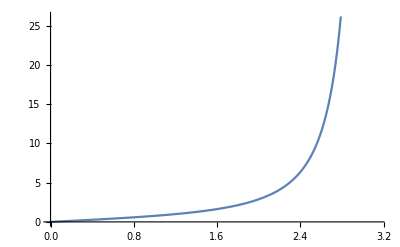

```mathematica
Plot[g[θ],{θ,0,π}]
```

```mathematica
geodesicI[t1_]:=geodesic[ {#,0,0}& ] /; t1==0;
geodesicI[t1_]:=Module[{},
blah;
blah;
blah
]/; t1>0;
geodesicI[t1_]:=Module[{},
blah;
blah;
blah
]/;t1<0;
```

## Introduction to Heisenberg Group Animations

## Animation Tools

```mathematica
standardGraphicsArguments:=Sequence[Axes->True,AxesStyle->Directive[Thin,White],AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-10,10},{-10,10},{-10,10}},Ticks->False,ViewAngle->Pi/8,ViewVertical->{0,0,1},Background->Black];
```

```mathematica
SetDirectory["C:\\Presentation Offline Folder"];
```

## Animation of Left-Multiplication “with a twist”

```mathematica
r=10.2;ϕ=.2π;ϕFinal=.6π;camHeight=9.9;
```

```mathematica
θ[t_]:=t/T ϕFinal+(T-t)/T ϕ
```

### Lattice Introduction Animation

```mathematica
stdLattice=Flatten[Table[{x,y,t},{x,-10,10},{y,-10,10},{t,-10,10}],2];
```

```mathematica
specialPoints={{{1,0,0}},{{0,1,0}}};
```

```mathematica
cameraPosition[t_]:={r Cos[θ[t]],r Sin[θ[t]],camHeight};
```

```mathematica
latticePlot=ListPointPlot3D[stdLattice,PlotStyle->{Orange,Thick,PointSize[.015]}];
```

```mathematica
specialPointsPlot=ListPointPlot3D[specialPoints,PlotStyle->{{Blue,Thick,PointSize[.03]},{Red,Thick,PointSize[.03]}}];
```

```mathematica
frame[t_]:=Show[{latticePlot,specialPointsPlot},standardGraphicsArguments,ViewVector->{cameraPosition[t],{0,0,0}},Background->Black];
```

```mathematica
T=1.6;fps=25;
```

```mathematica
(*  frames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["latticeIntro.mov",frames,"framerate"->fps]  *)
```

### Left Multiplication of Lattice: Initial Linear Shift

```mathematica
r=10.2;ϕFixed=.6π;camHeight=9.9;p={.5,-.4,.7};
```

```mathematica
cameraPositionFixed={r Cos[ϕFixed],r Sin[ϕFixed],camHeight};
```

```mathematica
linTrStdLattice[t_]:=Map[#+t/T p&,stdLattice];
```

```mathematica
linTrStdLatticePlot[t_]:=ListPointPlot3D[linTrStdLattice[t],PlotStyle->{Orange,Thick,PointSize[.015]}];
```

```mathematica
linTrSpecialPoints[t_]:={{{1,0,0}+t/T p},{{0,1,0}+t/T p}};
```

```mathematica
linTrSpecialPointsPlot[t_]:=ListPointPlot3D[linTrSpecialPoints[t],PlotStyle->{{Blue,Thick,PointSize[.03]},{Red,Thick,PointSize[.03]}}];
```

```mathematica
theArrow=Graphics3D[{Arrowheads[0.01],White,Thick,Arrow[{{0,0,0},p}]}];
```

```mathematica
frame[t_]:=Show[{linTrStdLatticePlot[t],linTrSpecialPointsPlot[t],theArrow},Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-5,5},{-5,5},{-5,5}},Ticks->False,ViewAngle->Pi/8,ViewVector->{cameraPositionFixed,{0,0,0}},Background->Black]
```

```mathematica
T=1.0;fps=25;
```

```mathematica
(*  frames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["linearShift.mov",frames,"framerate"->fps]  *)
```

### Left Multiplication of Lattice: the Twist

```mathematica
linTrPartialTwistedStdLattice[λ_]:=Map[λ l[p][#]+(1-λ)(#+p)&,stdLattice];
```

```mathematica
linTrPartialTwistedSpecialPoints[λ_]:={{λ l[p][{1,0,0}]+(1-λ)({1,0,0}+p)},{λ l[p][{0,1,0}]+(1-λ)({0,1,0}+p)}};
```

```mathematica
linTrPartialTwistedStdLatticePlot[t_]:=ListPointPlot3D[linTrPartialTwistedStdLattice[t/T],PlotStyle->{Orange,Thick,PointSize[.015]}];
```

```mathematica
linTrPartialTwistedSpecialPointsPlot[t_]:=ListPointPlot3D[linTrPartialTwistedSpecialPoints[t/T],PlotStyle->{{Blue,Thick,PointSize[.03]},{Red,Thick,PointSize[.03]}}];
```

```mathematica
frame[t_]:=Show[{linTrPartialTwistedStdLatticePlot[t],linTrPartialTwistedSpecialPointsPlot[t],theArrow},Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-5,5},{-5,5},{-5,5}},Ticks->False,ViewAngle->Pi/8,ViewVector->{cameraPositionFixed,{0,0,0}},Background->Black]
```

```mathematica
T=1.5;fps=25;
```

```mathematica
(*  frames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["twist1.mov",frames,"framerate"->fps]  *)
```

### Left Multiplication Example 2: Along t-Axis

```mathematica
p={0,0,1.2};ϕFixed=ϕFinal;
```

```mathematica
cameraPositionFixed={r Cos[ϕFixed],r Sin[ϕFixed],9.9};
```

```mathematica
linTrStdLattice[t_]:=Map[#+t/T p&,stdLattice];
```

```mathematica
linTrStdLatticePlot[t_]:=ListPointPlot3D[linTrStdLattice[t],PlotStyle->{Orange,Thick,PointSize[.015]}];
```

```mathematica
linTrSpecialPoints[t_]:={{{1,0,0}+t/T p},{{0,1,0}+t/T p}};
```

```mathematica
linTrSpecialPointsPlot[t_]:=ListPointPlot3D[linTrSpecialPoints[t],PlotStyle->{{Blue,Thick,PointSize[.03]},{Red,Thick,PointSize[.03]}}];
```

```mathematica
theArrow=Graphics3D[{Arrowheads[0.01],White,Thick,Arrow[{{0,0,0},p}]}];
```

```mathematica
frame[t_]:=Show[{linTrStdLatticePlot[t],linTrSpecialPointsPlot[t],theArrow},Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-5,5},{-5,5},{-5,5}},Ticks->False,ViewAngle->Pi/8,ViewVector->{cameraPositionFixed,{0,0,0}},Background->Black]
```

```mathematica
T=1;fps=25;
```

```mathematica
(*  frames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["leftMult2.mov",frames,"framerate"->fps]  *)
```

### Left Multiplication Example 3: Shift & Twist!

#### Linear Motion Frames

```mathematica
p={-0.5,-1.2,0};ϕFixed=ϕFinal;
```

```mathematica
cameraPositionFixed={r Cos[ϕFixed],r Sin[ϕFixed],9.9};
```

```mathematica
linTrStdLattice[t_]:=Map[#+t/T p&,stdLattice];
```

```mathematica
linTrStdLatticePlot[t_]:=ListPointPlot3D[linTrStdLattice[t],PlotStyle->{Orange,Thick,PointSize[.015]}];
```

```mathematica
linTrSpecialPoints[t_]:={{{1,0,0}+t/T p},{{0,1,0}+t/T p}};
```

```mathematica
linTrSpecialPointsPlot[t_]:=ListPointPlot3D[linTrSpecialPoints[t],PlotStyle->{{Blue,Thick,PointSize[.03]},{Red,Thick,PointSize[.03]}}];
```

```mathematica
theArrow=Graphics3D[{Arrowheads[0.01],White,Thick,Arrow[{{0,0,0},p}]}];
```

```mathematica
frame[t_]:=Show[{linTrStdLatticePlot[t],linTrSpecialPointsPlot[t],theArrow},Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-5,5},{-5,5},{-5,5}},Ticks->False,ViewAngle->Pi/8,ViewVector->{cameraPositionFixed,{0,0,0}},Background->Black]
```

```mathematica
T=1;fps=25;
```

```mathematica
(*  linearFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

#### Twist Frames

```mathematica
linTrPartialTwistedStdLattice[λ_]:=Map[λ l[p][#]+(1-λ)(#+p)&,stdLattice];
```

```mathematica
linTrPartialTwistedSpecialPoints[λ_]:={{λ l[p][{1,0,0}]+(1-λ)({1,0,0}+p)},{λ l[p][{0,1,0}]+(1-λ)({0,1,0}+p)}};
```

```mathematica
linTrPartialTwistedStdLatticePlot[t_]:=ListPointPlot3D[linTrPartialTwistedStdLattice[t/T],PlotStyle->{Orange,Thick,PointSize[.015]}];
```

```mathematica
linTrPartialTwistedSpecialPointsPlot[t_]:=ListPointPlot3D[linTrPartialTwistedSpecialPoints[t/T],PlotStyle->{{Blue,Thick,PointSize[.03]},{Red,Thick,PointSize[.03]}}];
```

```mathematica
frame[t_]:=Show[{linTrPartialTwistedStdLatticePlot[t],linTrPartialTwistedSpecialPointsPlot[t],theArrow},Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-5,5},{-5,5},{-5,5}},Ticks->False,ViewAngle->Pi/8,ViewVector->{cameraPositionFixed,{0,0,0}},Background->Black]
```

```mathematica
T=1;fps=25;
```

```mathematica
(*  twistFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

#### Complete Animation

```mathematica
(*  frames=linearFrames~Join~twistFrames;  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["leftMult3.mov",frames,"framerate"->fps] *)
```

## Animation of the Left-Invariant Vector Fields

```mathematica
r=10.2;fps=25;ϕ=.60;ϕFinal=2.0;camHeight=9.9;
```

### Lattice Introduction Animation

```mathematica
stdLattice=Flatten[Table[{x,y,t},{x,-10,10},{y,-10,10},{t,-10,10}],2];
```

```mathematica
specialPoints={{{1,0,0}},{{0,1,0}}};
```

```mathematica
θ[t_]:=t/T ϕFinal+(T-t)/T ϕ
```

```mathematica
cameraPosition[t_]:={r Cos[θ[t]],r Sin[θ[t]],camHeight};
```

```mathematica
latticePlot=ListPointPlot3D[stdLattice,PlotStyle->{Orange,Thick,PointSize[.015]}];
```

```mathematica
specialPointsPlot=ListPointPlot3D[specialPoints,PlotStyle->{{Blue,Thick,PointSize[.03]},{Red,Thick,PointSize[.03]}}];
```

```mathematica
frame[t_]:=Show[{latticePlot,specialPointsPlot},Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotRange->{{-5,5},{-5,5},{-5,5}},Ticks->False,ViewAngle->Pi/8,ViewVector->{cameraPosition[t],{0,0,0}},Background->Black];
```

```mathematica
T=2.4;fps=25;
```

```mathematica
(*  frames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["latticeIntro2.mov",frames,"framerate"->fps];  *)
```

### Just Some Curve, through a Fading Lattice

We animate a curve passing through the origin with given initial velocity “v”, over an interval from (-ϵ,ϵ).

```mathematica
v={-0.7,0.8,0.3};ϵ=0.9;ϕFixed=2.0;
```

```mathematica
cameraPositionFixed={r Cos[ϕFixed],r Sin[ϕFixed],camHeight};
```

#### The Curve

```mathematica
{a,b,c}=Table[RandomReal[],{3}];
```

```mathematica
γ[s_]:=v s+s^2{a,b,c};
```

```mathematica
partialCurvePlot[s_]:=ParametricPlot3D[γ[σ],{σ,-ϵ-.001,s}];
```

#### The Fading Lattice

```mathematica
fadingLatticePlot[t_]:=ListPointPlot3D[stdLattice,PlotStyle->{Orange,Thick,PointSize[0.015],Opacity[(T-t)/T]}];
```

#### Complete Animation

```mathematica
frame[t_]:=Show[{fadingLatticePlot[t],specialPointsPlot,partialCurvePlot[((2t)/T-1)ϵ]},standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];
```

```mathematica
T=1.2;fps=25;
```

```mathematica
(*  frames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["curve1.mov",frames,"framerate"->fps];  *)
```

### The Same Curve, with an Arrow, and undergoing Shift

#### Constants

We use the same constants from “Just some Curve”, adding now a point p for left-translation.

```mathematica
cameraPositionFixed={r Cos[ϕFixed],r Sin[ϕFixed],camHeight};
```

```mathematica
p={-1.1,-.75,.3};
```

#### Fixed Curve Graphic

```mathematica
γ[s_]:=v s+s^2{a,b,c};
```

```mathematica
fixedArrow=Graphics3D[{White,Thick,Arrowheads[0.01], Arrow[{{0,0,0},v}]}];
```

```mathematica
fixedCurvePlot=Show[ParametricPlot3D[γ[σ],{σ,-ϵ,ϵ}],fixedArrow];
```

#### Linear Motion Frames

```mathematica
darkGreen=RGBColor[0,0.5,0];
```

γLin[ t ] is a parametrized family of curves.

```mathematica
γLin[t_][s_]:=γ[s]+t/T p;
```

```mathematica
linArrow[t_]:=Arrow[{γLin[t][0],γLin[t][0]+(γLin[t])'[0]}];
```

```mathematica
linArrowPlot[t_]:=Graphics3D[{White,Thick,Arrowheads[0.01],linArrow[t]}];
```

```mathematica
linTrCurvePlot[t_]:=Show[ParametricPlot3D[γLin[t][σ],{σ,-ϵ,ϵ},PlotStyle->{Thin,darkGreen}],linArrowPlot[t]]
```

#### Complete Animation for Linear Shift

```mathematica
frame[t_]:=Show[{fixedCurvePlot,linTrCurvePlot[t]},standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}},Background->Black];
```

```mathematica
T=0.8;fps=25;
```

```mathematica
(*  inearFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

#### Twist Motion Frames

```mathematica
γTwist[λ_][s_]:=λ l[p][γ[s]]+(1-λ)(γ[s]+p);
```

```mathematica
twistArrow[t_]:=Arrow[{γTwist[t/T][0],γTwist[t/T][0]+(γTwist[t/T])'[0]}];
```

```mathematica
twistArrowPlot[t_]:=Graphics3D[{White,Thick,Arrowheads[0.01],twistArrow[t]}];
```

```mathematica
twistTrCurvePlot[t_]:=Show[ParametricPlot3D[γTwist[t/T][σ],{σ,-ϵ,ϵ},PlotStyle->{Thin,darkGreen}],twistArrowPlot[t]];
```

#### Complete Animation for Twist

```mathematica
T=1.2;fps=25;
```

```mathematica
frame[t_]:=Show[{fixedCurvePlot,twistTrCurvePlot[t]},standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}},Background->Black];
```

```mathematica
(*  twistFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

#### Curve Undergoing Shift-and-Twist

```mathematica
(*  frames=linearFrames~Join~twistFrames;  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["shiftAndTwistCurve.mov",frames,"framerate"->fps];  *)
```

### Production of X

#### Left-Translated Vector

```mathematica
r=10.2;ϕ=.60;camHeight=5.0;scaleFactor=0.4;
```

```mathematica
cameraPositionFixed={r Cos[ϕFixed],r Sin[ϕFixed],camHeight};
```

```mathematica
img1=Show[{Graphics3D[],specialPointsPlot,fixedArrow,twistArrowPlot[1.2]},standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];
```

```mathematica
img2=Show[{Graphics3D[],fixedArrow,twistArrowPlot[1.2]},standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];
```

```mathematica
(*  Export["emptyAxes.png",img1];  *)
```

```mathematica
(*  Export["emptyAxes2.png",img2];  *)
```

#### Initial x-Axis Sweep

```mathematica
γ=Interpolation[{{0,0},{1,0},{1.9,0},{2,0},{3,3},{4,7},{6,-7}},InterpolationOrder->3];
```

```mathematica
(*  Plot[γ[t],{t,0,7}] *)
```

```mathematica
entryTime[0]=0;
entryTime[x_]:=(entryTime[x]=(t/.FindRoot[γ[t]==x,{t,3}]))/;1≤x≤5;
entryTime[x_]:=(entryTime[x]=(t/.FindRoot[γ[t]==x,{t,5.5}]))/;-5≤x≤-1;
```

```mathematica
initialSweepXVals[t_]:=Select[Table[x,{x,-5,5}],entryTime[#]≤t&]
```

```mathematica
initialSweepArrows[t_]:=Map[XPlot[{#,0,0}]&,initialSweepXVals[t]];
```

```mathematica
frame[t_]:=Show[initialSweepArrows[t],XPlot[{γ[t],0,0}],standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}]
```

```mathematica
T=6;fps=25;
```

```mathematica
(*  initialSweepFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[initialSweepFrames,fps];  *)
```

#### Lateral X-Sweep

```mathematica
lateralSweepYVals[t_]:=Select[Table[y,{y,-5,5}],entryTime[#]≤t&];
```

```mathematica
lateralSweepArrows[t_]:=(Map[Table[XPlot[{x,#,0}],{x,-5,5}]&,lateralSweepYVals[t]]//Flatten)~Join~Table[XPlot[{x,γ[t],0}],{x,-5,5}];
```

```mathematica
frame[t_]:=Show[lateralSweepArrows[t],standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];
```

```mathematica
T=6;fps=25;
```

```mathematica
(*  lateralSweepFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[lateralSweepFrames,fps]  *)
```

For use later, we save the last graphic.

```mathematica
xCompletedSweepPlot=frame[6];
```

#### X-Sweep Animation

```mathematica
(*  frames=initialSweepFrames~Join~lateralSweepFrames;  *)
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["xSweep.mov",frames,"framerate"->fps];  *)
```

### Production of Y

#### Initial y-Axis Sweep

```mathematica
γ=Interpolation[{{0,0},{1,0},{1.9,0},{2,0},{3,3},{4,7},{6,-7}},InterpolationOrder->3];
```

```mathematica
(*  Plot[γ[t],{t,0,7}]  *)
```

```mathematica
Clear[entryTime]
entryTime[0]=0;
entryTime[s_]:=(entryTime[s]=(t/.FindRoot[γ[t]==s,{t,3}]))/;1≤s≤5;
entryTime[s_]:=(entryTime[s]=(t/.FindRoot[γ[t]==s,{t,5.5}]))/;-5≤s≤-1;
```

```mathematica
initialSweepYVals[t_]:=Select[Table[y,{y,-5,5}],entryTime[#]≤t&]
```

```mathematica
initialSweepArrows[t_]:=Map[YPlot[{0,#,0}]&,initialSweepYVals[t]];
```

```mathematica
frame[t_]:=Show[initialSweepArrows[t],YPlot[{0,γ[t],0}],standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}]
```

```mathematica
T=6;fps=25;
```

```mathematica
(*  initialSweepFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[initialSweepFrames,fps];  *)
```

#### Lateral Y-Sweep

```mathematica
lateralSweepXVals[t_]:=Select[Table[x,{x,-5,5}],entryTime[#]≤t&];
```

```mathematica
lateralSweepArrows[t_]:=(Map[Table[YPlot[{#,y,0}],{y,-5,5}]&,lateralSweepXVals[t]]//Flatten)~Join~Table[YPlot[{γ[t],y,0}],{y,-5,5}];
```

```mathematica
frame[t_]:=Show[lateralSweepArrows[t],standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];
```

```mathematica
T=6;fps=25;
```

```mathematica
(*  lateralSweepFrames=Table[frame[t],{t,0,T,1/fps}];  *)
```

```mathematica
yCompletedSweepPlot=frame[6];
```

```mathematica
(*  ListAnimate[lateralSweepFrames,fps]  *)
```

#### Y-Sweep Animation

```mathematica
frames=initialSweepFrames~Join~lateralSweepFrames;
```

```mathematica
(*  ListAnimate[frames,fps];  *)
```

```mathematica
(*  Export["ySweep.mov",frames,"framerate"->fps];  *)
```

### X and Y Together

```mathematica
img=Show[xCompletedSweepPlot,yCompletedSweepPlot,standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];
```

```mathematica
(*  Export["XAndYComplete.png",img];  *)
```

## Horizontal Distribution

### Preamble

We have the opportunity here to demonstrate how one travels through the Heisenberg Group “legally” - i.e., along the Horizontal Distribution.  In the first frame-set, we show the less-dramatic spread-out distribution, viewed from not-far outside.  

Then, the distribution contracts tight, so that viewers can see its tendency to reward clockwise motion from afar.  

The camera rotates around this in a circle.  

Note that this entire animation is parameterized by θ[ t ] and λ[ t ], so can be done in one frame set, just by tweaking the interpolation data for these functions.  

Now, we define a curve γ[ s ] that starts just below our camera position.  For a brief clip at high speed, the camera jerks down to look at the curve, which has just started drawing.  

As the curve draws, we watch it, and move with it.  Slow... then FAST down the loop .... then at a “medium pace” as we thread the horizontal distribution from within.  This will be parameterized by s[ t ].

### The Horizontal Distribution

#### Constants

```mathematica
r=10.2;ϕStart=.8π;ϕFinal=1.17π;camHeight=4.0;
cameraPositionFixed={r Cos[ϕStart],r Sin[ϕStart],camHeight};
θ[t_]:=(T-t)/T ϕStart+t/T ϕFinal;
cameraPosition[t_]:={r Cos[θ[t]],r Sin[θ[t]],camHeight};
```

```mathematica
scaleFactor=.2;
horDistPlotsXY=Flatten[Table[horDistPlot[{x0,y0,0}],{x0,-5,5},{y0,-5,5},{t0,-5,5}],2];
```

#### Horizontal Distribution on xy-Plane Image

```mathematica
(*  img=Show[horDistPlotsXY,standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];  *)
(*  Export["horDist1.png",img,ImageResolution->800]  *)
```

#### Full Horizontal Distribution with Scaling

```mathematica
horDistPlots[λ_]:=(scaleFactor=(.2)/5 λ+.1;Flatten[Table[horDistPlot[{x0,y0,t0}],{x0,-λ,λ,λ/5},{y0,-λ,λ,λ/5},{t0,-λ,λ,λ/5}],2]);
```

#### Full Horizontal Distribution Contraction Animation

```mathematica
T=4;fps=25;
```

```mathematica
λ=Interpolation[{{0,5},{1,5},{1.8,5},{2,5},{2.25,1},{2.45,1},{3,1},{4,1}},InterpolationOrder->2];
```

```mathematica
frame[t_]:=Show[horDistPlots[λ[t]],standardGraphicsArguments,ViewVector->{cameraPosition[t],{0,0,0}}];
```

```mathematica
(*  frames=Table[frame[t],{t,0,T,1/fps}]; *)
```

```mathematica
(*  ListAnimate[frames,fps]  *)
```

```mathematica
(*  Export["horDistContraction.mov",frames,"framerate"->fps,ImageResolution->800]; *)
```

### A Horizontal curve comes to play

```mathematica
r=10.2;camHeight=8;ϕFinal=1.17π
cameraPositionFixed={r Cos[ϕFinal],r Sin[ϕFinal],camHeight};
```

3.67566

```mathematica
TIntro=2;Δt=TIntro/3;P={-1,-1,-1};
```

```mathematica
θIntroInit=0;θIntroFinal=-π/2-ArcTan[3/4];θIntro[t_]:=t/TIntro θIntroFinal+(TIntro-t)/TIntro θIntroInit;x[t_]:=t/TIntro(-1)+(TIntro-t)/TIntro(-5);
γIntro[t_]:=Evaluate[{x[t],-4-5Cos[θIntro[t]],3+5Sin[θIntro[t]]}]/;0≤t≤TIntro;
```

```mathematica
THorThread=4;
θHorThread[t_]:=t/THorThread π;
γProjx[t_]:=-Cos[θHorThread[t]];γProjy[t_]:=-1+2Sin[θHorThread[t]];
γThread[t_]:={γProjx[t],γProjy[t]}~Join~{-1-2∫_0^t (γProjx[σ]γProjy'[σ]-γProjy[σ]γProjx'[σ])ⅆσ};
```

```mathematica
Clear[γ]
γ[t_]:=(γ[t]=γIntro[t])/;0≤t≤TIntro;
γ[t_]:=(γ[t]=γThread[t-TIntro])/;TIntro<t≤TIntro+THorThread;
```

```mathematica
(*  Show[specialPointsPlot,ParametricPlot3D[γ[t],{t,0,TIntro+THorThread}],standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}] *)
```

```mathematica
frame[t_]:=Show[horDistPlots[1],specialPointsPlot,ParametricPlot3D[γ[s],{s,0-.01,t}],standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}];
```

```mathematica
(*  T=TIntro+THorThread;fps=10;
frames=Table[frame[t],{t,0,T 1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps] *)
```

```mathematica
(*  Export["threadingCurve.mov",frames,"framerate"->fps]  *)
```

### We walk along a Horizontal Curve

```mathematica
Clear[γ,γ1,γ2,γ3]
```

```mathematica
P={-0.5,-8,-0.5};Q={-0.5,-1,-0.5};t1=5;t2=10;t3=13;
```

```mathematica
γ1=Interpolation[{{0,P},{t1,Q}},InterpolationOrder->1];
```

```mathematica
x[s_]:=0.1-0.6Cos[s];y[s_]:=-1+0.6Sin[s];
γ2Proj[s_]:={x[s],y[s]};
γ2[s_]:={x[s],y[s],-0.5-2∫_0^s (x[σ]y'[σ]-y[σ]x'[σ])ⅆσ};
```

```mathematica
R={0.7,-1,γ2[π][[3]]};S={0.7,-8,γ2[π][[3]]};
γ3=Interpolation[{{0,R},{3,S}},InterpolationOrder->1];
```

```mathematica
γ[t_]:=Piecewise[{{γ1[t], 0≤t≤t1}, {γ2[(t-t1)/(t2-t1)π], t1≤t≤t2}, {γ3[t-t2], t2≤t≤t3}}];
```

```mathematica
theCurve=ParametricPlot3D[γ[t],{t,0,t3}] ;
```

```mathematica
viewVector[t_]:={γ[t]+{0,0,.03},γ[t+.2]};
```

```mathematica
frame[t_]:=Show[theCurve,horDistPlots[1],standardGraphicsArguments,ViewVector->viewVector[t]];
```

```mathematica
T=t3;fps=25;
(*  frames=Table[frame[t],{t,0,T,1/fps}]; *)
```

```mathematica
(*  ListAnimate[frames,fps]  *)
```

```mathematica
(*  Export["walkingTheDistribution.mov",frames,"framerate"->fps]  *)
```

### Horizontal Curves and Their Projections

#### Constants

```mathematica
r=6.0;ϕFixed=-.15π;camHeight=6.0;diam=.65;
cameraPositionFixed={r Cos[ϕFixed],r Sin[ϕFixed],camHeight};
θ[t_]:=(T-t)/T ϕStart+t/T ϕFinal;
cameraPosition[t_]:={r Cos[θ[t]],r Sin[θ[t]],camHeight};
```

```mathematica
(*  scaleFactor=.2;
horDistPlotsXY=Flatten[Table[horDistPlot[{x0,y0,0}],{x0,-5,5},{y0,-5,5},{t0,-5,5}],2];  *)
```

#### Green’s Theorem

```mathematica
γPx[s_]:=diam Cos[π/2-s]^2;γPy[s_]:=diam Cos[π/2-s]Sin[π/2-s];
```

```mathematica
-4∫(γPx[s]γPy'[s]-γPy[s]γPx'[s])ⅆs
```

-4 (-0.21125 s+0.105625 Sin[2. s])

```mathematica
γt[s_]:=s/2-1/4 Sin[2 s]
```

```mathematica
γ[s_]:={γPx[s],γPy[s],γt[s]};
```

```mathematica
partialγCurve[t_]:=ParametricPlot3D[γ[s],{s,0,t},AxesStyle->Directive[Orange, 12]];
```

```mathematica
partialγPCurve[t_]:=ParametricPlot3D[{γPx[s],γPy[s],0},{s,0,t},PlotStyle->White];
```

```mathematica
frame[t_]:=Show[{partialγPCurve[t],partialγCurve[t]},standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}]
```

```mathematica
T=π;fps=25;
(*  frames=Table[frame[t],{t,0.01,T,1/fps}];  *)
```

```mathematica
(*  ListAnimate[frames,fps]  *)
```

```mathematica
(*  Export["greensTheorem.mov",frames,"framerate"->fps]  *)
```

```mathematica
circle=Graphics3D[{LightGray,Opacity[0.5],Cylinder[{{diam/2,0,-.001},{diam/2,0,.001}},diam/2]}];
```

```mathematica
(*  img=Show[{circle,frame[π]},standardGraphicsArguments,ViewVector->{cameraPositionFixed,{0,0,0}}]  *)
```

```mathematica
(*  Export["greensTheoremPic.png",img,ImageResolution->800];  *)
```

## Gromov’s Conjecture